```mathematica
foo = {{{1,2},{3,4},{5,6}},{{1,4},{3,5},{5,3}}}
```

{{{1,2},{3,4},{5,6}},{{1,4},{3,5},{5,3}}}

```mathematica
listableMin[foo]
```

{{1,2},{3,4},{5,3}}

```mathematica
Length[quarkData]
```

861

```mathematica
StandardDeviation[BulkdataTop]
```

{{0.,3.3838},{0.,3.2436},{0.,3.10665},{0.,2.97376},{0.,2.84605},{0.,2.72503},{0.,2.61275},{0.,2.51212},{0.,2.42714},{0.,2.36334},{0.,2.32787},{0.,2.32788},{0.,2.35802},{0.,2.35802},{0.,2.32788},{0.,2.32787},{0.,2.36334},{0.,2.42714},{0.,2.51212},{0.,2.61275},{0.,2.72503},{0.,2.84605},{0.,2.97376},{0.,3.10665},{0.,3.2436},{0.,3.3838}}

```mathematica
Mean[BulkdataTop]+StandardDeviation[BulkdataTop]
```

{{-6.25,13.1978},{-5.75,12.4276},{-5.25,11.6622},{-4.75,10.9028},{-4.25,10.1511},{-3.75,9.40939},{-3.25,8.68115},{-2.75,7.97127},{-2.25,7.28719},{-1.75,6.64056},{-1.25,6.05078},{-0.75,5.55372},{-0.25,5.22758},{0.25,5.22758},{0.75,5.55372},{1.25,6.05078},{1.75,6.64056},{2.25,7.28719},{2.75,7.97127},{3.25,8.68115},{3.75,9.40939},{4.25,10.1511},{4.75,10.9028},{5.25,11.6622},{5.75,12.4276},{6.25,13.1978}}

```mathematica
Mean[BulkdataTop]
```

{{-6.25,9.81396},{-5.75,9.18402},{-5.25,8.55556},{-4.75,7.92903},{-4.25,7.305},{-3.75,6.68436},{-3.25,6.0684},{-2.75,5.45916},{-2.25,4.86005},{-1.75,4.27722},{-1.25,3.72292},{-0.75,3.22584},{-0.25,2.86955},{0.25,2.86955},{0.75,3.22584},{1.25,3.72292},{1.75,4.27722},{2.25,4.86005},{2.75,5.45916},{3.25,6.0684},{3.75,6.68436},{4.25,7.305},{4.75,7.92903},{5.25,8.55556},{5.75,9.18402},{6.25,9.81396}}

```mathematica
listableMin[BulkdataTop]
```

{{0,7.82373},{0,7.29098},{0,6.75842},{0,6.2261},{0,5.6941},{0,5.16256},{0,4.63167},{0,4.10179},{0,3.5736},{0,3.0486},{0,2.53062},{0,2.03243},{0,1.61922},{0,1.61922},{0,2.03243},{0,2.53062},{0,3.0486},{0,3.5736},{0,4.10179},{0,4.63167},{0,5.16256},{0,5.6941},{0,6.2261},{0,6.75842},{0,7.29098},{0,7.82373}}

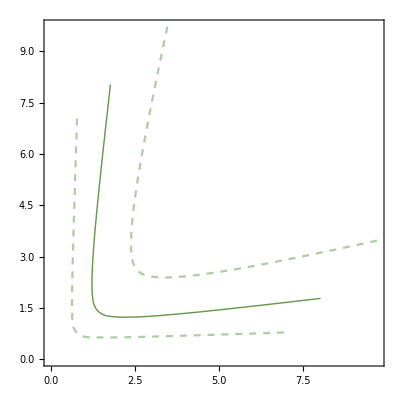

```mathematica
ListPlot[{
TurnLeft[Mean[#1]],
TurnLeft[Mean[#1]+StandardDeviation[#1]],
TurnLeft[listableMin[#1]]
},
PlotStyle->{
{Thick,#2},
{Dashed,Opacity[0.5],#2},
{Dashed,Opacity[0.5],#2}
}]& [BulkdataTop,colors[[6]]]
```

```mathematica
{
TurnLeft[Mean[#1]],
TurnLeft[Mean[#1]+StandardDeviation[#1]],
TurnLeft[Mean[#1]-listableMin[#1]]
}&[BulkdataTop]
```

{{{1.78198,8.03198},{1.71701,7.46701},{1.65278,6.90278},{1.58951,6.33951},{1.5275,5.7775},{1.46718,5.21718},{1.4092,4.6592},{1.35458,4.10458},{1.30503,3.55503},{1.26361,3.01361},{1.23646,2.48646},{1.23792,1.98792},{1.30978,1.55978},{1.55978,1.30978},{1.98792,1.23792},{2.48646,1.23646},{3.01361,1.26361},{3.55503,1.30503},{4.10458,1.35458},{4.6592,1.4092},{5.21718,1.46718},{5.7775,1.5275},{6.33951,1.58951},{6.90278,1.65278},{7.46701,1.71701},{8.03198,1.78198}},{{3.47388,9.72388},{3.33881,9.08881},{3.2061,8.4561},{3.07639,7.82639},{2.95053,7.20053},{2.82969,6.57969},{2.71557,5.96557},{2.61064,5.36064},{2.5186,4.7686},{2.44528,4.19528},{2.40039,3.65039},{2.40186,3.15186},{2.48879,2.73879},{2.73879,2.48879},{3.15186,2.40186},{3.65039,2.40039},{4.19528,2.44528},{4.7686,2.5186},{5.36064,2.61064},{5.96557,2.71557},{6.57969,2.82969},{7.20053,2.95053},{7.82639,3.07639},{8.4561,3.2061},{9.08881,3.33881},{9.72388,3.47388}},{{0.995116,0.995116},{0.946519,0.946519},{0.898574,0.898574},{0.851466,0.851466},{0.805451,0.805451},{0.760901,0.760901},{0.718363,0.718363},{0.678684,0.678684},{0.643226,0.643226},{0.614309,0.614309},{0.596146,0.596146},{0.596706,0.596706},{0.625165,0.625165},{0.625165,0.625165},{0.596706,0.596706},{0.596146,0.596146},{0.614309,0.614309},{0.643226,0.643226},{0.678684,0.678684},{0.718363,0.718363},{0.760901,0.760901},{0.805451,0.805451},{0.851466,0.851466},{0.898574,0.898574},{0.946519,0.946519},{0.995116,0.995116}}}